Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210603_bar_charts_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/pltcm_manipulated_64026.csv"];
```

Data for First and Second Half of Complete Data

```mathematica
Dimensions@datafull
```

{64026,12}

```mathematica
x=Round@Length@datafull/2;
{a,b}=Range[x,Length@datafull,x];
data1sthalf=Take[datafull,{1,a}];
data2ndhalf=Take[datafull,{a+1,b}];
stepsizewidth=11;
stepsizethickness=0.05;
```

Investigation of Constraints Impact in Real-life Production Events

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataFixedstep1=snetworkdatabinned[9,stepsizewidth,data1sthalf];
graphsandnodenumbers1=snetworkgraph[widthdataFixedstep1[[1]],widthdataFixedstep1[[2]],2,7,400,Green];
modularityvalues1=N@GraphAssortativity[graphsandnodenumbers1[[1]],FindGraphCommunities[graphsandnodenumbers1[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd1=randomizinggraphdegfxd[graphsandnodenumbers1[[1]]];
singlerandomerdrenmodularityvalues1=N@GraphAssortativity[singlerandomgraphsdegfxd1,FindGraphCommunities[singlerandomgraphsdegfxd1],"Normalized"->False];
singlerandomgraphscomm1=randomizinggraphmod[graphsandnodenumbers1[[1]]];
singlerandomcommmodularityvalues1=N@GraphAssortativity[singlerandomgraphscomm1,FindGraphCommunities[singlerandomgraphscomm1],"Normalized"->False];
Zscoresmodularity1=zscorefunctionfortwonullmodels[graphsandnodenumbers1[[1]]];
bucketnode11=graphsandnodenumbers1[[2]]]
```

{45.4255,85}

```mathematica
AbsoluteTiming[widthdataFixedstep2=snetworkdatabinned[9,stepsizewidth,data2ndhalf];
graphsandnodenumbers12=snetworkgraph[widthdataFixedstep2[[1]],widthdataFixedstep2[[2]],2,7,400,Green];
modularityvalues12=N@GraphAssortativity[graphsandnodenumbers12[[1]],FindGraphCommunities[graphsandnodenumbers12[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd12=randomizinggraphdegfxd[graphsandnodenumbers12[[1]]];
singlerandomerdrenmodularityvalues12=N@GraphAssortativity[singlerandomgraphsdegfxd12,FindGraphCommunities[singlerandomgraphsdegfxd12],"Normalized"->False];
singlerandomgraphscomm12=randomizinggraphmod[graphsandnodenumbers12[[1]]];
singlerandomcommmodularityvalues12=N@GraphAssortativity[singlerandomgraphscomm12,FindGraphCommunities[singlerandomgraphscomm12],"Normalized"->False];Zscoresmodularity12=zscorefunctionfortwonullmodels[graphsandnodenumbers12[[1]]];
bucketnode12=graphsandnodenumbers12[[2]]]
```

{57.9281,85}

```mathematica
AbsoluteTiming[widthdataFixedstep3=snetworkdatabinned[9,stepsizewidth,datafull];
graphsandnodenumbers13=snetworkgraph[widthdataFixedstep3[[1]],widthdataFixedstep3[[2]],2,7,400,Green];
modularityvalues13=N@GraphAssortativity[graphsandnodenumbers13[[1]],FindGraphCommunities[graphsandnodenumbers13[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd13=randomizinggraphdegfxd[graphsandnodenumbers13[[1]]];
singlerandomerdrenmodularityvalues13=N@GraphAssortativity[singlerandomgraphsdegfxd13,FindGraphCommunities[singlerandomgraphsdegfxd13],"Normalized"->False];
singlerandomgraphscomm13=randomizinggraphmod[graphsandnodenumbers13[[1]]];
singlerandomcommmodularityvalues13=N@GraphAssortativity[singlerandomgraphscomm13,FindGraphCommunities[singlerandomgraphscomm13],"Normalized"->False];
Zscoresmodularity13=zscorefunctionfortwonullmodels[graphsandnodenumbers13[[1]]];
bucketnode13=graphsandnodenumbers13[[2]]]
```

{72.1195,86}

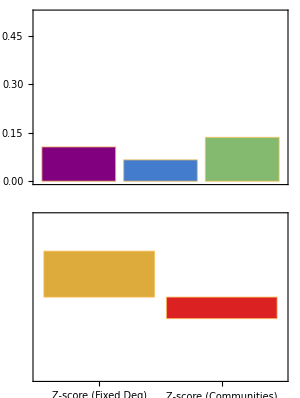
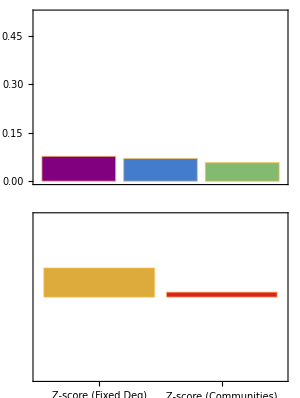
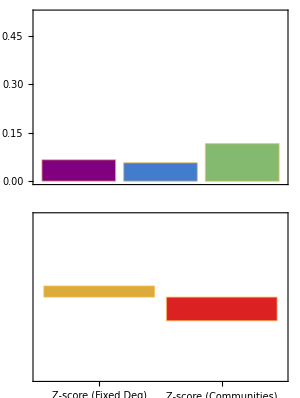

```mathematica
modvalues={modularityvalues1,modularityvalues12,modularityvalues13};rndmoddegrees={singlerandomerdrenmodularityvalues1,singlerandomerdrenmodularityvalues12,singlerandomerdrenmodularityvalues13};rndmodcomm={singlerandomcommmodularityvalues1,singlerandomcommmodularityvalues12,singlerandomcommmodularityvalues13};
zscoredegrees={Zscoresmodularity1[[1]],Zscoresmodularity12[[1]],Zscoresmodularity13[[1]]};zscorecomm={Zscoresmodularity1[[2]],Zscoresmodularity12[[2]],Zscoresmodularity13[[2]]};labels={"Modularity","Sng. Rnd. Mod.\n(Fixed Deg)","Sng. Rnd. Mod.\n(Communities)","Z-score\n(Fixed Deg)","Z-score\n(Communities)"};
colors={{Purple,RGBColor[{0.266122,0.486664,0.802529}],RGBColor[{0.513417,0.72992,0.440682}]},{RGBColor[{0.863512,0.670771,0.236564}],RGBColor[{0.857359,0.131106,0.132128}]}};imagesize=ImageSize->300;
zscorerange={If[Positive[(zscoreminmax=MinMax[Flatten@{zscoredegrees,zscorecomm}])[[1]]],0,zscoreminmax[[1]]],zscoreminmax[[2]]};
modularityrange1=Max[Flatten@{modvalues,rndmoddegrees,rndmodcomm}];
zscorerange1=zscorerange;
zscorerange={-10,10};
modularityrange={0,0.52};
Legended[Framed[Row[{GraphicsColumn[{BarChart[{modvalues[[1]],rndmoddegrees[[1]],rndmodcomm[[1]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[1]],zscorecomm[[1]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1],Magnify[GraphicsColumn[{BarChart[{modvalues[[3]],rndmoddegrees[[3]],rndmodcomm[[3]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[3]],zscorecomm[[3]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1],1.1],GraphicsColumn[{BarChart[{modvalues[[2]],rndmoddegrees[[2]],rndmodcomm[[2]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[2]],zscorecomm[[2]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1]}],FrameMargins->15,FrameStyle->DotDashed],{Placed["First Half",{0.155,0.99}],Placed["Complete Data",{0.505,0.99}],Placed["Second Half",{0.86,0.99}]}]
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataFixedstep1=snetworkdatabinned[10,stepsizethickness,data1sthalf];
graphsandnodenumbers2=snetworkgraph[thicknessdataFixedstep1[[1]],thicknessdataFixedstep1[[2]],2,7,400,Green];
modularityvalues2=N@GraphAssortativity[graphsandnodenumbers2[[1]],FindGraphCommunities[graphsandnodenumbers2[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd2=randomizinggraphdegfxd[graphsandnodenumbers2[[1]]];
singlerandomerdrenmodularityvalues2=N@GraphAssortativity[singlerandomgraphsdegfxd2,FindGraphCommunities[singlerandomgraphsdegfxd2],"Normalized"->False];
singlerandomgraphscomm2=randomizinggraphmod[graphsandnodenumbers2[[1]]];
singlerandomcommmodularityvalues2=N@GraphAssortativity[singlerandomgraphscomm2,FindGraphCommunities[singlerandomgraphscomm2],"Normalized"->False];
Zscoresmodularity2=zscorefunctionfortwonullmodels[graphsandnodenumbers2[[1]]];
bucketnode21=graphsandnodenumbers2[[2]]]
```

{32.1164,60}

```mathematica
AbsoluteTiming[thicknessdataFixedstep2=snetworkdatabinned[10,stepsizethickness,data2ndhalf];
graphsandnodenumbers22=snetworkgraph[thicknessdataFixedstep2[[1]],thicknessdataFixedstep2[[2]],2,7,400,Green];
modularityvalues22=N@GraphAssortativity[graphsandnodenumbers22[[1]],FindGraphCommunities[graphsandnodenumbers22[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd22=randomizinggraphdegfxd[graphsandnodenumbers22[[1]]];
singlerandomerdrenmodularityvalues22=N@GraphAssortativity[singlerandomgraphsdegfxd22,FindGraphCommunities[singlerandomgraphsdegfxd22],"Normalized"->False];
singlerandomgraphscomm22=randomizinggraphmod[graphsandnodenumbers22[[1]]];
singlerandomcommmodularityvalues22=N@GraphAssortativity[singlerandomgraphscomm22,FindGraphCommunities[singlerandomgraphscomm22],"Normalized"->False];Zscoresmodularity22=zscorefunctionfortwonullmodels[graphsandnodenumbers22[[1]]];
bucketnode22=graphsandnodenumbers22[[2]]]
```

{29.0161,55}

```mathematica
AbsoluteTiming[thicknessdataFixedstep3=snetworkdatabinned[10,stepsizethickness,datafull];
graphsandnodenumbers23=snetworkgraph[thicknessdataFixedstep3[[1]],thicknessdataFixedstep3[[2]],2,7,400,Green];
modularityvalues23=N@GraphAssortativity[graphsandnodenumbers23[[1]],FindGraphCommunities[graphsandnodenumbers23[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd23=randomizinggraphdegfxd[graphsandnodenumbers23[[1]]];
singlerandomerdrenmodularityvalues23=N@GraphAssortativity[singlerandomgraphsdegfxd23,FindGraphCommunities[singlerandomgraphsdegfxd23],"Normalized"->False];
singlerandomgraphscomm23=randomizinggraphmod[graphsandnodenumbers23[[1]]];
singlerandomcommmodularityvalues23=N@GraphAssortativity[singlerandomgraphscomm23,FindGraphCommunities[singlerandomgraphscomm23],"Normalized"->False];
Zscoresmodularity23=zscorefunctionfortwonullmodels[graphsandnodenumbers23[[1]]];
bucketnode23=graphsandnodenumbers23[[2]]]
```

{42.2166,62}

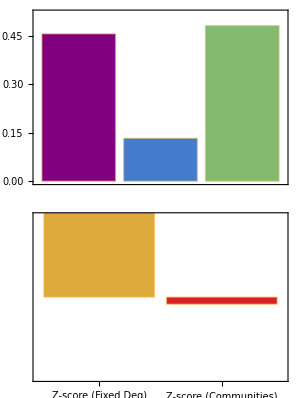
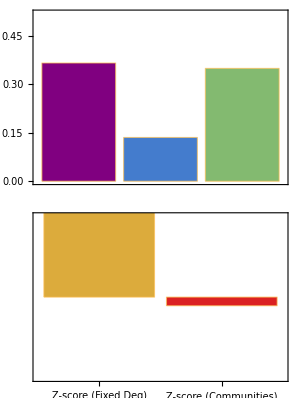
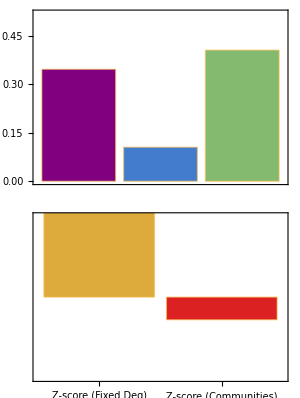

```mathematica
modvalues={modularityvalues2,modularityvalues22,modularityvalues23};rndmoddegrees={singlerandomerdrenmodularityvalues2,singlerandomerdrenmodularityvalues22,singlerandomerdrenmodularityvalues23};rndmodcomm={singlerandomcommmodularityvalues2,singlerandomcommmodularityvalues22,singlerandomcommmodularityvalues23};zscoredegrees={Zscoresmodularity2[[1]],Zscoresmodularity22[[1]],Zscoresmodularity23[[1]]};zscorecomm={Zscoresmodularity2[[2]],Zscoresmodularity22[[2]],Zscoresmodularity23[[2]]};labels={"Modularity","Sng. Rnd. Mod.\n(Fixed Deg)","Sng. Rnd. Mod.\n(Communities)","Z-score\n(Fixed Deg)","Z-score\n(Communities)"};
colors={{Purple,RGBColor[{0.266122,0.486664,0.802529}],RGBColor[{0.513417,0.72992,0.440682}]},{RGBColor[{0.863512,0.670771,0.236564}],RGBColor[{0.857359,0.131106,0.132128}]}};imagesize=ImageSize->300;
zscorerange={If[Positive[(zscoreminmax=MinMax[Flatten@{zscoredegrees,zscorecomm}])[[1]]],0,zscoreminmax[[1]]],zscoreminmax[[2]]};
modularityrange2=Max[Flatten@{modvalues,rndmoddegrees,rndmodcomm}];
zscorerange2=zscorerange;
zscorerange={-10,10};
modularityrange={0,0.52};
Legended[Framed[Row[{GraphicsColumn[{BarChart[{modvalues[[1]],rndmoddegrees[[1]],rndmodcomm[[1]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[1]],zscorecomm[[1]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1],Magnify[GraphicsColumn[{BarChart[{modvalues[[3]],rndmoddegrees[[3]],rndmodcomm[[3]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[3]],zscorecomm[[3]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1],1.1],GraphicsColumn[{BarChart[{modvalues[[2]],rndmoddegrees[[2]],rndmodcomm[[2]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[2]],zscorecomm[[2]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1]}],FrameMargins->15,FrameStyle->DotDashed],{Placed["First Half",{0.155,0.99}],Placed["Complete Data",{0.505,0.99}],Placed["Second Half",{0.86,0.99}]}]
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataFixedbucket1=snetworkdatafxdbucket[9,bucketnode11,data1sthalf];
graphsandnodenumbers3=snetworkgraph[widthdataFixedbucket1[[1]],widthdataFixedbucket1[[2]],2,7,400,Green];
modularityvalues3=N@GraphAssortativity[graphsandnodenumbers3[[1]],FindGraphCommunities[graphsandnodenumbers3[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd3=randomizinggraphdegfxd[graphsandnodenumbers3[[1]]];
singlerandomerdrenmodularityvalues3=N@GraphAssortativity[singlerandomgraphsdegfxd3,FindGraphCommunities[singlerandomgraphsdegfxd3],"Normalized"->False];
singlerandomgraphscomm3=randomizinggraphmod[graphsandnodenumbers3[[1]]];
singlerandomcommmodularityvalues3=N@GraphAssortativity[singlerandomgraphscomm3,FindGraphCommunities[singlerandomgraphscomm3],"Normalized"->False];
Zscoresmodularity3=zscorefunctionfortwonullmodels[graphsandnodenumbers3[[1]]];]
```

{57.8934,Null}

```mathematica
AbsoluteTiming[widthdataFixedbucket2=snetworkdatafxdbucket[9,bucketnode12,data2ndhalf];
graphsandnodenumbers32=snetworkgraph[widthdataFixedbucket2[[1]],widthdataFixedbucket2[[2]],2,7,400,Green];
modularityvalues32=N@GraphAssortativity[graphsandnodenumbers32[[1]],FindGraphCommunities[graphsandnodenumbers32[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd32=randomizinggraphdegfxd[graphsandnodenumbers32[[1]]];
singlerandomerdrenmodularityvalues32=N@GraphAssortativity[singlerandomgraphsdegfxd32,FindGraphCommunities[singlerandomgraphsdegfxd32],"Normalized"->False];
singlerandomgraphscomm32=randomizinggraphmod[graphsandnodenumbers32[[1]]];
singlerandomcommmodularityvalues32=N@GraphAssortativity[singlerandomgraphscomm32,FindGraphCommunities[singlerandomgraphscomm32],"Normalized"->False];Zscoresmodularity32=zscorefunctionfortwonullmodels[graphsandnodenumbers32[[1]]];]
```

{68.0378,Null}

```mathematica
AbsoluteTiming[widthdataFixedbucket3=snetworkdatafxdbucket[9,bucketnode13,datafull];
graphsandnodenumbers33=snetworkgraph[widthdataFixedbucket3[[1]],widthdataFixedbucket3[[2]],2,7,400,Green];
modularityvalues33=N@GraphAssortativity[graphsandnodenumbers33[[1]],FindGraphCommunities[graphsandnodenumbers33[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd33=randomizinggraphdegfxd[graphsandnodenumbers33[[1]]];
singlerandomerdrenmodularityvalues33=N@GraphAssortativity[singlerandomgraphsdegfxd33,FindGraphCommunities[singlerandomgraphsdegfxd33],"Normalized"->False];
singlerandomgraphscomm33=randomizinggraphmod[graphsandnodenumbers33[[1]]];
singlerandomcommmodularityvalues33=N@GraphAssortativity[singlerandomgraphscomm33,FindGraphCommunities[singlerandomgraphscomm33],"Normalized"->False];
Zscoresmodularity33=zscorefunctionfortwonullmodels[graphsandnodenumbers33[[1]]];]
```

{123.939,Null}

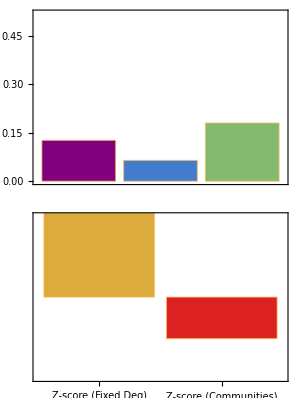
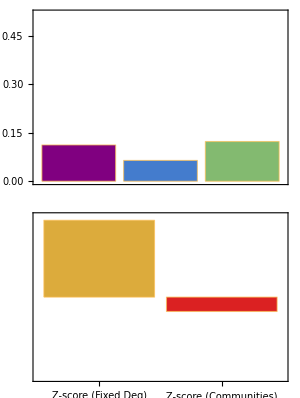
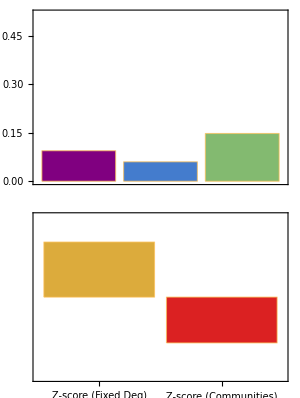

```mathematica
modvalues={modularityvalues3,modularityvalues32,modularityvalues33};rndmoddegrees={singlerandomerdrenmodularityvalues3,singlerandomerdrenmodularityvalues32,singlerandomerdrenmodularityvalues33};rndmodcomm={singlerandomcommmodularityvalues3,singlerandomcommmodularityvalues32,singlerandomcommmodularityvalues33};zscoredegrees={Zscoresmodularity3[[1]],Zscoresmodularity32[[1]],Zscoresmodularity33[[1]]};zscorecomm={Zscoresmodularity3[[2]],Zscoresmodularity32[[2]],Zscoresmodularity33[[2]]};labels={"Modularity","Sng. Rnd. Mod.\n(Fixed Deg)","Sng. Rnd. Mod.\n(Communities)","Z-score\n(Fixed Deg)","Z-score\n(Communities)"};
colors={{Purple,RGBColor[{0.266122,0.486664,0.802529}],RGBColor[{0.513417,0.72992,0.440682}]},{RGBColor[{0.863512,0.670771,0.236564}],RGBColor[{0.857359,0.131106,0.132128}]}};imagesize=ImageSize->300;
zscorerange={If[Positive[(zscoreminmax=MinMax[Flatten@{zscoredegrees,zscorecomm}])[[1]]],0,zscoreminmax[[1]]],zscoreminmax[[2]]};
modularityrange3=Max[Flatten@{modvalues,rndmoddegrees,rndmodcomm}];
zscorerange3=zscorerange;
zscorerange={-10,10};
modularityrange={0,0.52};
Legended[Framed[Row[{GraphicsColumn[{BarChart[{modvalues[[1]],rndmoddegrees[[1]],rndmodcomm[[1]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[1]],zscorecomm[[1]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1],Magnify[GraphicsColumn[{BarChart[{modvalues[[3]],rndmoddegrees[[3]],rndmodcomm[[3]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[3]],zscorecomm[[3]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1],1.1],GraphicsColumn[{BarChart[{modvalues[[2]],rndmoddegrees[[2]],rndmodcomm[[2]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[2]],zscorecomm[[2]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1]}],FrameMargins->15,FrameStyle->DotDashed],{Placed["First Half",{0.155,0.99}],Placed["Complete Data",{0.505,0.99}],Placed["Second Half",{0.86,0.99}]}]
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataFixedbucket1=snetworkdatafxdbucket[10,bucketnode21,data1sthalf];
graphsandnodenumbers4=snetworkgraph[thicknessdataFixedbucket1[[1]],thicknessdataFixedbucket1[[2]],2,7,400,Green];
modularityvalues4=N@GraphAssortativity[graphsandnodenumbers4[[1]],FindGraphCommunities[graphsandnodenumbers4[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd4=randomizinggraphdegfxd[graphsandnodenumbers4[[1]]];
singlerandomerdrenmodularityvalues4=N@GraphAssortativity[singlerandomgraphsdegfxd4,FindGraphCommunities[singlerandomgraphsdegfxd4],"Normalized"->False];
singlerandomgraphscomm4=randomizinggraphmod[graphsandnodenumbers4[[1]]];
singlerandomcommmodularityvalues4=N@GraphAssortativity[singlerandomgraphscomm4,FindGraphCommunities[singlerandomgraphscomm4],"Normalized"->False];
Zscoresmodularity4=zscorefunctionfortwonullmodels[graphsandnodenumbers4[[1]]];]
```

{48.1422,Null}

```mathematica
AbsoluteTiming[thicknessdataFixedbucket2=snetworkdatafxdbucket[10,bucketnode22,data2ndhalf];
graphsandnodenumbers42=snetworkgraph[thicknessdataFixedbucket2[[1]],thicknessdataFixedbucket2[[2]],2,7,400,Green];
modularityvalues42=N@GraphAssortativity[graphsandnodenumbers42[[1]],FindGraphCommunities[graphsandnodenumbers42[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd42=randomizinggraphdegfxd[graphsandnodenumbers42[[1]]];
singlerandomerdrenmodularityvalues42=N@GraphAssortativity[singlerandomgraphsdegfxd42,FindGraphCommunities[singlerandomgraphsdegfxd42],"Normalized"->False];
singlerandomgraphscomm42=randomizinggraphmod[graphsandnodenumbers42[[1]]];
singlerandomcommmodularityvalues42=N@GraphAssortativity[singlerandomgraphscomm42,FindGraphCommunities[singlerandomgraphscomm42],"Normalized"->False];Zscoresmodularity42=zscorefunctionfortwonullmodels[graphsandnodenumbers42[[1]]];]
```

{54.0025,Null}

```mathematica
AbsoluteTiming[thicknessdataFixedbucket3=snetworkdatafxdbucket[10,bucketnode23,datafull];
graphsandnodenumbers43=snetworkgraph[thicknessdataFixedbucket3[[1]],thicknessdataFixedbucket3[[2]],2,7,400,Green];
modularityvalues43=N@GraphAssortativity[graphsandnodenumbers43[[1]],FindGraphCommunities[graphsandnodenumbers43[[1]]],"Normalized"->False];
singlerandomgraphsdegfxd43=randomizinggraphdegfxd[graphsandnodenumbers43[[1]]];
singlerandomerdrenmodularityvalues43=N@GraphAssortativity[singlerandomgraphsdegfxd43,FindGraphCommunities[singlerandomgraphsdegfxd43],"Normalized"->False];
singlerandomgraphscomm43=randomizinggraphmod[graphsandnodenumbers43[[1]]];
singlerandomcommmodularityvalues43=N@GraphAssortativity[singlerandomgraphscomm43,FindGraphCommunities[singlerandomgraphscomm43],"Normalized"->False];
Zscoresmodularity43=zscorefunctionfortwonullmodels[graphsandnodenumbers43[[1]]];]
```

{64.906,Null}

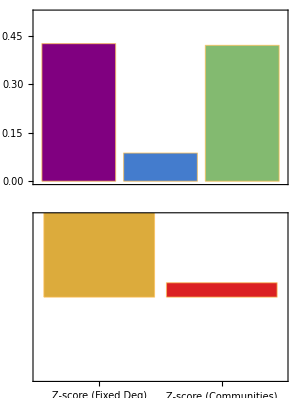
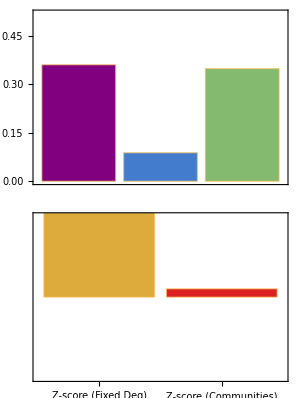
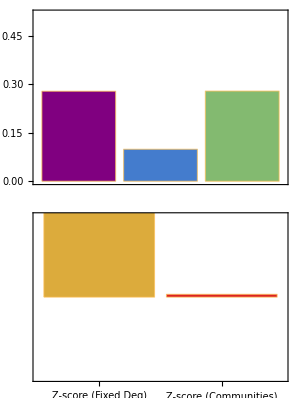

```mathematica
modvalues={modularityvalues4,modularityvalues42,modularityvalues43};rndmoddegrees={singlerandomerdrenmodularityvalues4,singlerandomerdrenmodularityvalues42,singlerandomerdrenmodularityvalues43};rndmodcomm={singlerandomcommmodularityvalues4,singlerandomcommmodularityvalues42,singlerandomcommmodularityvalues43};zscoredegrees={Zscoresmodularity4[[1]],Zscoresmodularity42[[1]],Zscoresmodularity43[[1]]};zscorecomm={Zscoresmodularity4[[2]],Zscoresmodularity42[[2]],Zscoresmodularity43[[2]]};labels={"Modularity","Sng. Rnd. Mod.\n(Fixed Deg)","Sng. Rnd. Mod.\n(Communities)","Z-score\n(Fixed Deg)","Z-score\n(Communities)"};
colors={{Purple,RGBColor[{0.266122,0.486664,0.802529}],RGBColor[{0.513417,0.72992,0.440682}]},{RGBColor[{0.863512,0.670771,0.236564}],RGBColor[{0.857359,0.131106,0.132128}]}};imagesize=ImageSize->300;
zscorerange={If[Positive[(zscoreminmax=MinMax[Flatten@{zscoredegrees,zscorecomm}])[[1]]],0,zscoreminmax[[1]]],zscoreminmax[[2]]};
modularityrange4=Max[Flatten@{modvalues,rndmoddegrees,rndmodcomm}];
zscorerange4=zscorerange;
zscorerange={-10,10};
modularityrange={0,0.52};
Legended[Framed[Row[{GraphicsColumn[{BarChart[{modvalues[[1]],rndmoddegrees[[1]],rndmodcomm[[1]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[1]],zscorecomm[[1]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1],Magnify[GraphicsColumn[{BarChart[{modvalues[[3]],rndmoddegrees[[3]],rndmodcomm[[3]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[3]],zscorecomm[[3]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1],1.1],GraphicsColumn[{BarChart[{modvalues[[2]],rndmoddegrees[[2]],rndmodcomm[[2]]},ChartStyle->colors[[1]],ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},modularityrange}],BarChart[{zscoredegrees[[2]],zscorecomm[[2]]},ChartStyle->colors[[2]](*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},zscorerange},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},imagesize,Spacings->1]}],FrameMargins->15,FrameStyle->DotDashed],{Placed["First Half",{0.155,0.99}],Placed["Complete Data",{0.505,0.99}],Placed["Second Half",{0.86,0.99}]}]
```

```mathematica
(* Max@{modularityrange1,modularityrange2,modularityrange3,modularityrange4}
MinMax@{zscorerange1,zscorerange2,zscorerange3,zscorerange4}
0.376
{-7.45,46.7}*)
```